## Figure 7

### Trajectory, Variance and Power Spectrum (Parameter set 1)

-Graphics-

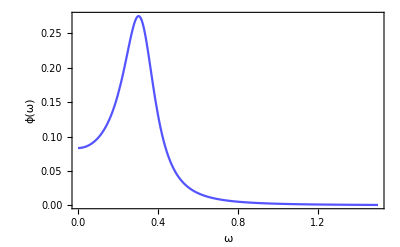

```mathematica
(* Define parameter values *)
params={NT->1000,maxT->10000,dt->0.05,maxRuns->10};

(* Define community matrix *)
A={{-0.1,-1},{0.1,-0.1}};

(* Define simple noise matrix *)
B=1/NT IdentityMatrix[2];

(* Define covariance matrix for fluctuations *)
Σ={{Σ11,Σ12},{Σ12,Σ22}};

(* Solve Lyapunov Equation for covariance matrix *)
ΣSol1=Solve[A.Σ+Σ.Transpose[A]+B==0,DeleteDuplicates[Flatten[Σ]]][[1]];

(* Solve for power spectra *)
PSMAT1=Inverse[A-I*ω*IdentityMatrix[2]].B.Inverse[Transpose[A]+I*ω*IdentityMatrix[2]]//FullSimplify;

(* Use Euyler-Marayuma method to simulate SDEs for OU process *)
traj=ConstantArray[0,Round[maxT/dt/.params]];
traj[[1]]={dt,0,0}/.params;
For[i=2,i≤Round[maxT/dt/.params],i++,
x=traj[[i-1]][[2]]+(A.traj[[i-1]][[2;;3]])[[1]]*dt+√(dt/NT)*RandomVariate[NormalDistribution[]]/.params;
y=traj[[i-1]][[3]]+(A.traj[[i-1]][[2;;3]])[[2]]*dt+√(dt/NT)*RandomVariate[NormalDistribution[]]/.params;

traj[[i]]={i*dt,x,y}/.params;
];

(* Plot quantities *)
trajPlot1=Show[
ListLinePlot[traj[[All,{1,2}]],PlotStyle->LightOrange,Frame->True,PlotRange->{-0.5,1},FrameStyle->12,FrameLabel->{Style["t",16],Style["ξ",16]},
Epilog->Inset[
ListLinePlot[traj[[1;;Round[200/dt/.params],{1,2}]],PlotStyle->{Orange,Thickness[0.003]},Frame->True,FrameTicks->False,AspectRatio->0.2,ImageSize->200,PlotRange->{-0.3,0.3}]
,{1275*5,0.75}]],
Plot[{√Σ11,-√Σ11}/.ΣSol1/.params,{t,0,maxT/.params},PlotStyle->{Black,Dashed}]
]

PSPlot1=Plot[PSMAT1[[1,1]]/.params,{ω,0,1.5},PlotRange->All,PlotStyle->Lighter[Blue],Frame->True,PlotRange->{-0.5,1},FrameStyle->12,FrameLabel->{Style["ω",16],Style["ϕ(ω)",16]},
Epilog->Inset[
Show[
Histogram[RandomSample[traj[[All,2]],4000],25,"PDF",PlotRange->{{-0.6,0.6},{0,2.6}},Frame->True,FrameLabel->{Style["ξ",14],Style["P_st(ξ)",14]},FrameTicks->None],
Plot[PDF[NormalDistribution[0,√(Σ11/.ΣSol2/.params)],z],{z,-0.6,0.6},PlotRange->All,PlotStyle->{Black,Dashed}]
],
{1.,0.17}]
]
```

### Trajectory, Variance and Power Spectrum (Parameter set 2)

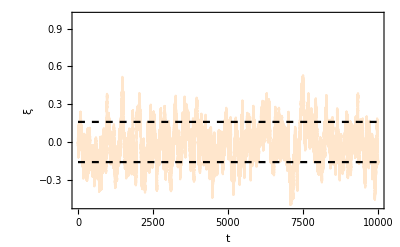

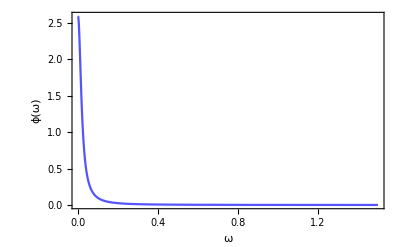

```mathematica
(* Define parameter values *)
params={NT->1000,maxT->10000,dt->0.05,maxRuns->10};

A={{-0.019642857142857142,0},{0.1,-0.1}};

B=1/NT IdentityMatrix[2];

Eigenvalues[A];

Σ={{Σ11,Σ12},{Σ12,Σ22}};
ΣSol2=Solve[A.Σ+Σ.Transpose[A]+B==0,DeleteDuplicates[Flatten[Σ]]][[1]];

PSMAT2=Inverse[A-I*ω*IdentityMatrix[2]].B.Inverse[Transpose[A]+I*ω*IdentityMatrix[2]]//FullSimplify;

traj=ConstantArray[0,Round[maxT/dt/.params]];
traj[[1]]={dt,0,0}/.params;
For[i=2,i≤Round[maxT/dt/.params],i++,
x=traj[[i-1]][[2]]+(A.traj[[i-1]][[2;;3]])[[1]]*dt+√(dt/NT)*RandomVariate[NormalDistribution[]]/.params;
y=traj[[i-1]][[3]]+(A.traj[[i-1]][[2;;3]])[[2]]*dt+√(dt/NT)*RandomVariate[NormalDistribution[]]/.params;

traj[[i]]={i*dt,x,y}/.params;
]

trajPlot2=Show[
ListLinePlot[traj[[All,{1,2}]],PlotStyle->LightOrange,Frame->True,PlotRange->{-0.5,1},FrameStyle->12,FrameLabel->{Style["t",16],Style["ξ",16]},
Epilog->Inset[
ListLinePlot[traj[[1;;Round[200/dt/.params],{1,2}]],PlotStyle->{Orange,Thickness[0.003]},Frame->True,FrameTicks->False,AspectRatio->0.2,ImageSize->200,PlotRange->{-0.3,0.3}]
,{1275*5,0.75}]],
Plot[{√Σ11,-√Σ11}/.ΣSol2/.params,{t,0,maxT/.params},PlotStyle->{Black,Dashed}]
]

PSPlot2=Plot[PSMAT2[[1,1]]/.params,{ω,0,1.5},PlotRange->All,PlotStyle->Lighter[Blue],Frame->True,PlotRange->{-0.5,1},FrameStyle->12,FrameLabel->{Style["ω",16],Style["ϕ(ω)",16]},
Epilog->Inset[
Show[
Histogram[RandomSample[traj[[All,2]],4000],25,"PDF",PlotRange->{{-0.6,0.6},{0,2.6}},Frame->True,FrameLabel->{Style["ξ",14],Style["P_st(ξ)",14]},FrameTicks->None],
Plot[PDF[NormalDistribution[0,√(Σ11/.ΣSol2/.params)],z],{z,-0.6,0.6},PlotRange->All,PlotStyle->{Black,Dashed}]
],
{1.,1.6}]
]
```

### Autocorrelations (Parameter set 1 & 2)

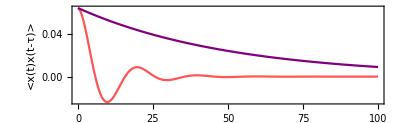

```mathematica
fourierPSMAT1=Evaluate[(FourierTransform[PSMAT1[[1,1]],ω,t]//FullSimplify)/.params];

fourierPSMAT2=Evaluate[(FourierTransform[PSMAT2[[1,1]],ω,t]//FullSimplify)/.params];

autoCorrPlot=Plot[{Re[fourierPSMAT1],Re[fourierPSMAT2]},{t,0,100},PlotRange->All,PlotStyle->{Lighter[Red],Purple},PlotLegends->{Style["Upper panels",14],Style["Lower panels",14]},Frame->True,FrameStyle->10,FrameLabel->{Style["τ",14],Style["<x(t)x(t-τ)>",14]},AspectRatio->1/(2GoldenRatio)]
```